This notebook is intended for you all to gain an intuition for what real life random walks actually look like. We’ll do this by looking at ensembles of independent randomly walking particles, and visualizing the final distribution of all of these particles. Using computers we can dispense of simplifying assumptions, like having equal sized steps, and instead draw our steps from any probability distribution we please! I highly encourage you to play around with the code (Try different distributions for the step size; come up with your own code for visualizing the paths; do a more quantitative data analysis of the endpoints of the particles; extend the simulation to higher dimensions). If you have any questions you can email me at anooppraturu@gmail.com. Also, feel free to share this notebook with whoever. Happy simulating!

```mathematica
(*We model our steps as a normally distributed random variable*)
step:=RandomReal[NormalDistribution[0,1]]
```

```mathematica
(*To simulate the walk we simply generate a bunch of independent steps, and then add them up to get the path of the particle. This function returns an array which tells you the position of the particle at each step*)
(*The parameter n is the number of steps in the walk*)
Walk[n_]:=Prepend[Accumulate[Table[step,{n}]],0]
```

```mathematica
(*Example walk:*)
Walk[10]
```

{0,-0.660287,-0.410837,-1.88633,-3.02645,-3.95471,-3.48704,-3.26643,-3.51831,-3.1377,-3.83791}

That’s basically it! The simulation itself was literally 2 lines, the rest is just visualizing these paths. If you don’t understand the remaining bits of code I wouldn’t worry about it, they’re just to make pretty pictures. It would be a great exercise for you to come up with your own way to visualize it.

```mathematica
(*Draws a line corresponding to the path of the particle. Since this is in 1d we can take the y direction to be time and the x direction to be space. So even though it's 1d the paths will look like elongated squiggles in 2d. The function also returns the endpoint of the particle so we can make a histogram of these values later on. The path is colored by how far away its final position is rom the origin.*)
(*N is again the number of steps in the walk*)
Walkplt[N_]:=
Module[{a=Walk[N],c},
c=ColorData["StarryNightColors"][Abs[Last[a]/(3*Sqrt[N])]];
a=Transpose[{a,Range[N+1]-(N+1)}];
{Last[a][[1]],Graphics[{c,Line[a]}]}
]
```

```mathematica
(*Makes a histogram of the final positions of an ensemble of random walks. The data for the final positions is given as "dat"*)
Hist[dat_]:=Module[{u=Max[dat],l=Min[dat],dx,bins,y,x},
dx=(u-l)/25;
bins=Table[x,{x,l,u-dx/2,dx}];
y=BinCounts[dat,{bins}];
x=ListConvolve[{0.5,0.5},bins];
Graphics[MapThread[{#3,Rectangle[{#1,0},{#1+dx,#2}]}&,{x,y,Map[ColorData["StarryNightColors"],2*Abs[x]/(u-l)]}],ImageSize->Large]
]
```

```mathematica
(*N: number of steps
r: number of particles
simulates r walks of N steps, plots all of the paths on top of each other and puts a histogram on top
*)
Ensemble[N_,r_]:=
Module[{data=Table[Walkplt[N],{r}],
paths,ends},
paths=data[[All,2]];
ends=data[[All,1]];
Show[{Hist[ends],paths}]]
```

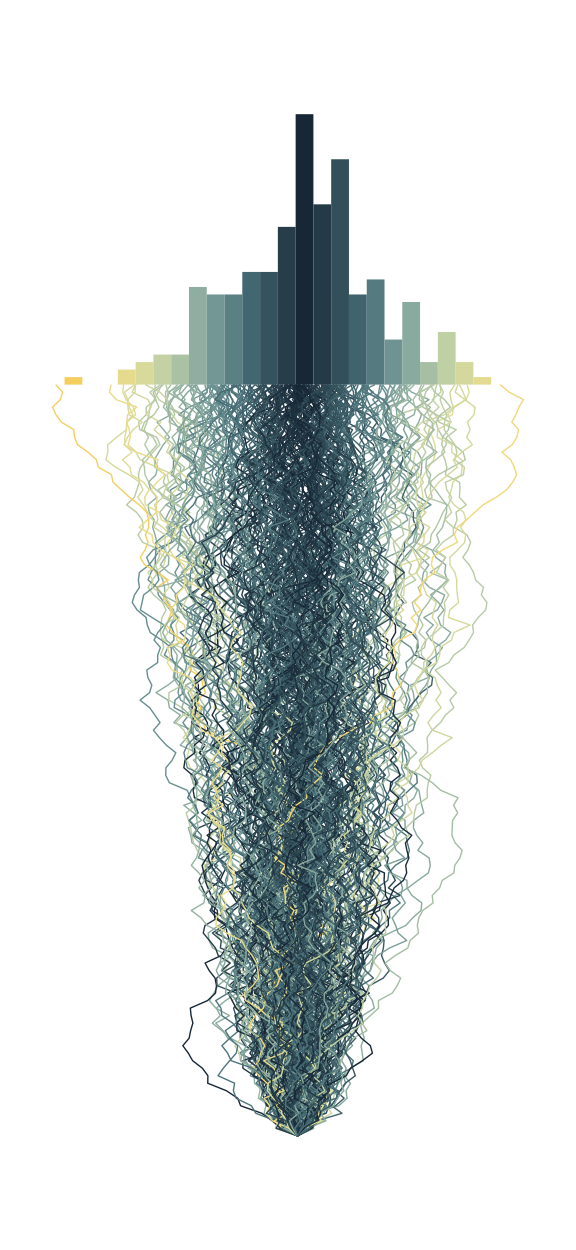

```mathematica
(*Simulate away!*)
Ensemble[100,250]
```